```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

# Generalities

## Generic

### Functions

Function to turn P into Q

```mathematica
PtoQ[P_]:=(P-p^2)/(p(1-p))//FullSimplify;
```

Delta function

```mathematica
Delta[x_]:=If[x==0,1,0]
```

### Define graphs

#### Island model, dispersal graph with self replacement

```mathematica
G12IM=({{(1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9}, {(1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9}, {(1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3}, {m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3}, {m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/3, (1-m)/3, (1-m)/3}});
Nin=3;
Ndemes=4;
```

#### Island model, dispersal graph without self replacement

```mathematica
G12IMnoself=({{0, (1-m)/2, (1-m)/2, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9}, {(1-m)/2, 0, (1-m)/2, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9}, {(1-m)/2, (1-m)/2, 0, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, 0, (1-m)/2, (1-m)/2, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, (1-m)/2, 0, (1-m)/2, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, (1-m)/2, (1-m)/2, 0, m/9, m/9, m/9, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, 0, (1-m)/2, (1-m)/2, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/2, 0, (1-m)/2, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/2, (1-m)/2, 0, m/9, m/9, m/9}, {m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, 0, (1-m)/2, (1-m)/2}, {m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/2, 0, (1-m)/2}, {m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, m/9, (1-m)/2, (1-m)/2, 0}});
```

#### Island model, dispersal graph, generic

```mathematica
G12IMgeneric=({{dself, din, din, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {din, dself, din, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {din, din, dself, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, dself, din, din, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, din, dself, din, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, din, din, dself, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, dself, din, din, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, din, dself, din, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, din, din, dself, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, dself, din, din}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, din, dself, din}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, din, din, dself}});
Nin=3;
Ndemes=4;
```

#### Island model, interaction graph : only within demes, with self interactions

```mathematica
GEIM=({{1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/3, 1/3, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/3, 1/3, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/3, 1/3, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/3, 1/3, 1/3}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/3, 1/3, 1/3}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/3, 1/3, 1/3}});
```

#### Island model, interaction graph without self interactions

```mathematica
GEIMnoself=({{0, 1/2, 1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 0, 1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/2, 1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 0, 1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 1/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/2, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/2, 0, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/2, 1/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2, 1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2, 0, 1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2, 1/2, 0}});
```

#### Island model, interaction graph, generic

```mathematica
GE12IMgeneric=({{eself, ein, ein, eout, eout, eout, eout, eout, eout, eout, eout, eout}, {ein, eself, ein, eout, eout, eout, eout, eout, eout, eout, eout, eout}, {ein, ein, eself, eout, eout, eout, eout, eout, eout, eout, eout, eout}, {eout, eout, eout, eself, ein, ein, eout, eout, eout, eout, eout, eout}, {eout, eout, eout, ein, eself, ein, eout, eout, eout, eout, eout, eout}, {eout, eout, eout, ein, ein, eself, eout, eout, eout, eout, eout, eout}, {eout, eout, eout, eout, eout, eout, eself, ein, ein, eout, eout, eout}, {eout, eout, eout, eout, eout, eout, ein, eself, ein, eout, eout, eout}, {eout, eout, eout, eout, eout, eout, ein, ein, eself, eout, eout, eout}, {eout, eout, eout, eout, eout, eout, eout, eout, eout, eself, ein, ein}, {eout, eout, eout, eout, eout, eout, eout, eout, eout, ein, eself, ein}, {eout, eout, eout, eout, eout, eout, eout, eout, eout, ein, ein, eself}});
```

#### Generic Q matrix

```mathematica
Q12generic=({{1, Qin, Qin, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, 1, Qin, Qin, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1}});
```

### Other

```mathematica
G10generic=({{dself, din, din, din, din, dout, dout, dout, dout, dout}, {din, dself, din, din, din, dout, dout, dout, dout, dout}, {din, din, dself, din, din, dout, dout, dout, dout, dout}, {din, din, din, dself, din, dout, dout, dout, dout, dout}, {din, din, din, din, dself, dout, dout, dout, dout, dout}, {dout, dout, dout, dout, dout, dself, din, din, din, din}, {dout, dout, dout, dout, dout, din, dself, din, din, din}, {dout, dout, dout, dout, dout, din, din, dself, din, din}, {dout, dout, dout, dout, dout, din, din, din, dself, din}, {dout, dout, dout, dout, dout, din, din, din, din, dself}});
```

```mathematica
Q10generic=({{1, Qin, Qin, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, 1, Qin, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, 1, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, Qin, 1, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, Qin, Qin, 1}});
```

```mathematica
GE10generic=G10generic/.{dself->eself,dout->eout,din->ein};
```

# IDB - Finding Q

## Moran

### Previous results

#### Calculations

Formula

```mathematica
PIM[r1_,r2_]:=CC/(n d)(1/μ+1/(1-(1-μ)(1-m-m/(d-1)))(Delta[r2]d-1)+Delta[r2]d(Delta[r1]n-1))+p^2
```

Find the constant term

```mathematica
solCC=Solve[PIM[0,0]==p,CC]//FullSimplify
```

{{CC→-(n (-1+p) p μ (-d m+μ+d (-1+m) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))}}

Formula with explicit constant term

```mathematica
PPIM[r1_,r2_]:=PIM[r1,r2]/.solCC⟦1⟧
```

Define Pin and Pout

```mathematica
PPIM[0,0]//FullSimplify
PinM=PPIM[2,0]//FullSimplify
PoutM=PPIM[2,1]//FullSimplify
```

p

(p (-(-1+d) μ (1+(-1+n p) μ)+m (-1+μ) (1+d (-1+n p) μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

(p (-(-1+d) p μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) p μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

#### Results

```mathematica
PinM=(p (-(-1+d) μ (1+(-1+n p) μ)+m (-1+μ) (1+d (-1+n p) μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
```

```mathematica
PoutM=(p (-(-1+d) p μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) p μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
```

```mathematica
QinM0=PtoQ[PinM]//FullSimplify;
QoutM0=PtoQ[PoutM]//FullSimplify;
```

### Numerical version

#### Function to find Q numerically

```mathematica
NGetQM[G_,Ν_,n_,p_,μ_]:=Module[{QT,eqs,vars,sols,QTs},(*
G is the dispersal graph,
Ν is the size of the population,
n is the degree of the graph,
p is the mutation biais,
μ is the mutation probability.
*)

(* Initialize the PT matrix *)
Do[Subscript[Q, i,j]=0;Subscript[Q, i,j]=.,{i,1,Ν},{j,1,Ν}];
QT=Table[Subscript[Q, i,j],{i,1,Ν},{j,1,Ν}];
Do[QT⟦i,i⟧=1,{i,1,Ν}]; (* Subscript[Q, i,i]= 1 *)
Do[QT⟦i,j⟧=Subscript[Q, j,i],{j,1,Ν-1},{i,j+1,Ν}]; (* Because Q is symmetric *)

eqs=Flatten[Table[Subscript[Q, i,j]==(1-μ)/(2 n)(Sum[G⟦l,j⟧QT⟦l,i⟧+G⟦l,i⟧QT⟦l,j⟧,{l,1,Ν}]),{i,1,Ν-1},{j,i+1,Ν}]];

vars=Flatten[Table[Subscript[Q, i,j],{i,1,Ν-1},{j,i+1,Ν}]];
sols=NSolve[eqs,vars];

QTs=QT/.sols⟦1⟧;
QTs]
```

#### Parameters

```mathematica
them=0.3;
thep=0.2;
theμ=0.1;
prms={d->4,n->3,p->thep,μ->theμ,m->them}
```

{d→4,n→3,p→0.2,μ→0.1,m→0.3}

#### With self replacement

```mathematica
Q12M=NGetQM[G12IM/.m->them,12,1,thep,theμ];
Q12inM=Q12M⟦1,2⟧
QinM3/.withselfreplacement/.prms
QinM/.prms
```

0.510638

ReplaceAll::reps: {withselfreplacement} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

QinM3/.withselfreplacement

QinM

#### Without self replacement

```mathematica
Q12Mns=NGetQM[G12IMnoself/.m->them,12,1,thep,theμ];
Q12inMns=Q12Mns⟦1,2⟧
QinM3/.noselfreplacement/.prms
```

0.596314

ReplaceAll::reps: {noselfreplacement} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

QinM3/.noselfreplacement

### New results

#### Generic equations

Replacements for dispersal probabilities, depending on whether there is self-replacement or not

```mathematica
noselfreplacement={dself->0,din->(1-m)/(n-1),dout->m/(d n - n)};
withselfreplacement={dself->(1-m)/n,din->(1-m)/n,dout->m/(d n - n)};
```

Generic equations for Q using the results on 2D graphs

```mathematica
QselfM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(n-1)+1/(1-(1-μ)(1-m-m/(d-1)))(d-1)+1/(1-(1-μ)(dself-din))(d-1)(n-1))
```

(λ ((-1+n)/(1-(-din+dself) (1-μ))+((-1+d) (-1+n))/(1-(-din+dself) (1-μ))+(-1+d)/(1-(1-m-m/(-1+d)) (1-μ))+1/μ) μ)/(d n)

```mathematica
QinM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(-1)+1/(1-(1-μ)(1-m-m/(d-1)))(d-1)+1/(1-(1-μ)(dself-din))(d-1)(-1));
QoutM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(-1)+1/(1-(1-μ)(1-m-m/(d-1)))(-1)+1/(1-(1-μ)(dself-din)));
```

Find λ using Qself == 1

```mathematica
theλM=λ/.Solve[QselfM2==1,λ]⟦1⟧//FullSimplify
```

(n (1+din+dself (-1+μ)-din μ) (-d m+μ+d (-1+m) μ))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

Replace λ in the equations for Qin and Qout

```mathematica
QinM=QinM2/.λ-> theλM//FullSimplify
QoutM=QoutM2/.λ-> theλM//FullSimplify
```

((-1+μ) ((-1+d) (1+din-dself) μ+m (1+din-dself-(d+din-dself) μ)))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

(m (-1+μ) (1+din+dself (-1+μ)-din μ))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

#### Equations with self replacement

```mathematica
QinMs=QinM/.withselfreplacement//FullSimplify
QoutMs=QoutM/.withselfreplacement//FullSimplify
```

-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

Simplify the way the equations are written (human - firendly versions)

```mathematica
QinMs-((1-μ) (d μ(1-m)-μ+m ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))//FullSimplify
```

0

```mathematica
QoutMs-(m (1-μ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))//FullSimplify
```

0

Check that this is the same as previously found

```mathematica
QinMs-QinM0//FullSimplify
```

0

```mathematica
QoutMs-QoutM0//FullSimplify
```

0

Check limit behaviour

```mathematica
Limit[QoutMs,d->∞]//FullSimplify
```

0

```mathematica
Limit[QinMs,d->∞]//FullSimplify
%/.μ->0//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

(1-m)/(1+m (-1+n))

```mathematica
Limit[QinMs,μ->0]//FullSimplify
```

1

```mathematica
Series[QinMs,{μ,0,1}]
```

1-d n μ+O[μ]^2

#### Equations without Self - replacement

```mathematica
QinMw=QinM/.noselfreplacement//FullSimplify
QoutMw=QoutM/.noselfreplacement//FullSimplify
```

((-1+μ) (m^2 (-1+μ)+(-1+d) n μ+m (n-d n μ)))/(m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ))

(m (n+m (-1+μ)-μ) (-1+μ))/(m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ))

Simplify the way they are written

```mathematica
QinMw-((1-μ) (d n μ(1-m)+(m-μ) n-m^2 (1-μ)))/(+(d-1) n μ (1+(n-2) μ)+m n (1-μ) (1+d (n-2) μ)-m^2 (1-μ)^2)//FullSimplify
```

0

```mathematica
QoutMw-(m (n+m (-1+μ)-μ) (1-μ))/(+(d-1) n μ (1+(n-2) μ)+m n (1-μ) (1+d (n-2) μ)-m^2 (1-μ)^2)//FullSimplify
```

0

Limit behavior

```mathematica
Limit[QinMw,d->∞]//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-2+n) (-1+μ)-(-2+n) μ)

```mathematica
Limit[QoutMw,d->∞]
```

0

## Wright - Fisher

### Does not work

```mathematica
eQinWF=(1-μ)^2((2 din dself + (n-2) din^2 + (Ν-n) dout^2)+(*
*)(dself^2+2(n-2) dself din + (n^2-3n+3) din^2+(Ν-n)(n-1)dout^2)Qin+(*
*)(Ν-n)dout(2 dself + 2(n-1) din + (Ν-2n) dout)Qout)
```

(1-μ)^2 (2 din dself+din^2 (-2+n)+dout^2 (-n+Ν)+dout Qout (-n+Ν) (2 dself+2 din (-1+n)+dout (-2 n+Ν))+Qin (dself^2+2 din dself (-2+n)+din^2 (3-3 n+n^2)+dout^2 (-1+n) (-n+Ν)))

```mathematica
eQoutWF=(1-μ)^2((2 dself dout + 2 (n-1)din dout + (Ν-2n)dout^2)+(*
*)(2(n-1) dself dout + 2(n-1)^2 din dout + (Ν-2n)(n-1)dout^2)Qin+(*
*)(dself^2+(n-1)dself din + (Ν-2n)dself dout + (n-1)din(dself + (n-1)din+(Ν-2n)dout)+(Ν-n)dout(dself+(n-1)din+(Ν-2n)dout))Qout)
```

(1-μ)^2 (2 dout dself+2 din dout (-1+n)+dout^2 (-2 n+Ν)+Qin (2 dout dself (-1+n)+2 din dout (-1+n)^2+dout^2 (-1+n) (-2 n+Ν))+Qout (dself^2+din dself (-1+n)+dout dself (-2 n+Ν)+din (-1+n) (dself+din (-1+n)+dout (-2 n+Ν))+dout (-n+Ν) (dself+din (-1+n)+dout (-2 n+Ν))))

```mathematica
sols=Solve[{Qin==eQinWF, Qout==eQoutWF}/.{dself->(1-m)/n,din->(1-m)/n, dout->m/(Ν-n)}/.Ν->n d,{Qin,Qout}]//FullSimplify
```

{{Qin→-((-1+μ)^2 (-3 (-1+d) d m^3 (-1+μ)^2+d^2 m^4 (-1+μ)^2-(-1+d)^3 (-2+μ) μ-(-1+d)^2 m^2 (-2+(-2+d) (-2+μ) μ)+(-1+d)^2 m (1+(-1+2 d) (-2+μ) μ)))/((2+d (-2+m))^2 m^2 (-1+n) (-1+μ)^4+(-1+d) (m (-1+μ)^2-(-1+d) (-2+μ) μ) (1+2 m (-1+n) (-1+μ)^2-(-1+n) (-2+μ) μ+d (-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ))),Qout→((-1+d) (2+d (-2+m)) m (-1+μ)^2)/(-3 (-1+d) d m^3 (-1+n) (-1+μ)^4+d^2 m^4 (-1+n) (-1+μ)^4-(-1+d)^2 m^2 (-1+n) (-1+μ)^2 (-2+(-2+d) (-2+μ) μ)-(-1+d)^3 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)+(-1+d)^2 m (-1+μ)^2 (-1+(-1+2 d) (-1+n) (-2+μ) μ))}}

```mathematica
sols/.μ->0//FullSimplify
```

{{Qin→-(1+2 m+d (-2+m (-4+3 m)+d (1+(-2+m) (-1+m) m)))/(-1+d^2 (-1+(-2+m) (-1+m) m (-1+n))+d (2+m (-4+3 m) (-1+n))+2 m (-1+n)),Qout→((-1+d) (2+d (-2+m)))/(-1+d^2 (-1+(-2+m) (-1+m) m (-1+n))+d (2+m (-4+3 m) (-1+n))+2 m (-1+n))}}

### Previous version

#### Results

```mathematica
PinWF=p (p-((-1+p) (-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)));
```

```mathematica
PoutWF=p (p-((-1+p) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)));
```

```mathematica
QinWF0=(PinWF-p^2)/(p(1-p))//FullSimplify;
QoutWF0=(PoutWF-p^2)/(p(1-p))//FullSimplify;
```

### Check numerically

```mathematica
NGetQWF[G_,Ν_,n_,p_,μ_]:=Module[{QT,eqs,vars,sols,QTs},(*
G is the dispersal graph,
Ν is the size of the population,
n is the degree of the graph,
p is the mutation biais,
μ is the mutation probability.
*)

(* Initialize the QT matrix *)
Do[Subscript[Q, i,j]=0;Subscript[Q, i,j]=.,{i,1,Ν},{j,1,Ν}];
QT=Table[Subscript[Q, i,j],{i,1,Ν},{j,1,Ν}];
Do[QT⟦i,i⟧=1,{i,1,Ν}]; (* Subscript[Q, i,i]=1 *)
Do[QT⟦i,j⟧=Subscript[Q, j,i],{j,1,Ν-1},{i,j+1,Ν}]; (* Because Q is symmetric *)

eqs=Flatten[Table[Subscript[Q, i,j]==(1-μ)^2/n^2(Sum[G⟦l,j⟧G⟦k,i⟧QT⟦k,l⟧,{l,1,Ν},{k,1,Ν}]),{i,1,Ν-1},{j,i+1,Ν}]];

vars=Flatten[Table[Subscript[Q, i,j],{i,1,Ν-1},{j,i+1,Ν}]];
sols=NSolve[eqs,vars];

QTs=QT/.sols⟦1⟧;
QTs]
```

With self replacement

```mathematica
tmp=NGetQWF[G12IM/.m->them,12,1,thep,theμ];
```

```mathematica
tmp⟦1,2⟧
```

0.314209

```mathematica
QinWFs/.prms
```

QinWFs

```mathematica
tmp⟦1,10⟧
QoutWFs/.prms
```

0.220112

QoutWFs

Without self replacement

```mathematica
tmp2=NGetQWF[G12IMnoself/.m->them,12,1,thep,theμ];
```

```mathematica
tmp2⟦1,2⟧
```

0.27517

```mathematica
QinWFw/.prms
```

QinWFw

```mathematica
tmp2⟦1,10⟧
QoutWFw/.prms
```

0.209558

QoutWFw

### New results

#### Generic

```mathematica
QselfWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)+1/(1-(1-μ)^2(dself-din)^2)(n-1)d+1/(1-(1-μ)^2(1-m-m/(d-1))^2)(d-1));
QinWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)-1/(1-(1-μ)^2(dself-din)^2)d+1/(1-(1-μ)^2(1-m-m/(d-1))^2)(d-1));
QoutWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)-1/(1-(1-μ)^2(1-m-m/(d-1))^2));
```

Find λ using Qself == 1

```mathematica
λWF=λ/.Solve[QselfWF2==1,λ]⟦1⟧
```

(d n)/((1/(1-(1-μ)^2)+(d (-1+n))/(1-(-din+dself)^2 (1-μ)^2)+(-1+d)/(1-(1-m-m/(-1+d))^2 (1-μ)^2)) μ)

Replace λ in the equations

```mathematica
QinWF=QinWF2/.λ->λWF//FullSimplify
QoutWF=QoutWF2/.λ->λWF//FullSimplify
```

(-d/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((d (-1+n))/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((d (-1+n))/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

#### With Self Replacement

```mathematica
QinWFs=QinWF/.withselfreplacement//FullSimplify
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
QinWFs-QinWF0//FullSimplify
```

0

```mathematica
QoutWFs=QoutWF/.withselfreplacement//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
QoutWFs-QoutWF0//FullSimplify
```

0

#### Without Self Replacement

```mathematica
QinWFw=QinWF/.noselfreplacement//FullSimplify
```

((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

```mathematica
QoutWFw=QoutWF/.noselfreplacement//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

# Expected Frequency Equations

## Moran, Birth - Death

### Generic equations

#### β

```mathematica
βBDD=(1-μ)(eself+(n-1)ein Qin + (n d-n)eout Qout);
```

```mathematica
βBDI=dself eself + (n-1)din ein+(n d -n )dout eout(*
*)+ (n-1)(din eself + dself ein +(n-2)din ein + (n d -n)dout eout)Qin (*
*)+(n d - n)(dself eout + (n-1)din eout + dout eself+(n-1)dout ein+(n d -2n)dout eout)Qout(*
*)-μ/(n d)(1+(n-1)Qin+(n d -n)Qout)(eself+(n-1)ein+(n d-n)eout);
```

```mathematica
factorBD=(p(1-p))/μ
```

((1-p) p)/μ

```mathematica
βBD=factorBD(βBDD-βBDI);
```

#### γ

```mathematica
γBDD=1-μ;
```

```mathematica
γBDI=dself+(n-1)din Qin+(n d-n)dout Qout-μ/(n d)(1+(n-1)Qin+(n d-n)Qout);
```

```mathematica
γBD=factorBD(γBDD-γBDI)//FullSimplify
```

((-1+p) p (d n (-1+dself+din (-1+n) Qin+(-1+d) dout n Qout)+(-1+Qin+n (d-Qin+Qout-d Qout)) μ))/(d n μ)

## Moran, Death-Birth

### Generic equations

#### β

```mathematica
βDBD=βBDD
```

(eself+ein (-1+n) Qin+eout (-n+d n) Qout) (1-μ)

```mathematica
βDBI=(1-μ)(1*dself dself eself*1(*
02*)+(n-1)dself din ein *1(*
03*)+(n d-n)dself dout eout *1(*
04*)+(n-1)dself dself ein Qin(*
05*)+(n-1) dself din eself Qin(*
06*)+(n-1)(n-2)dself din ein Qin(*
07*)+(n-1)(n d-n) dself dout eout Qin(*
08*)+(n d -n)dself dself eout Qout(*
09*)+(n d -n)(n-1) dself din eout Qout(*
10*)+(n d -n)dself dout eself Qout(*
11*)+(n d -n)(n-1) dself dout ein Qout(*
12*)+(n d -n)(n d-2n) dself dout eout Qout(*
13*)+(n-1)din dself eself Qin(*
14*)+(n-1) din din ein Qin(*
15*)+(n-1)(n-2)din din ein Qin (*
16*)+(n-1)(n d -n)din dout eout Qin(*
17*)+(n-1)din dself ein (*
18*)+(n-1)din din eself(*
19*)+(n-1)(n-2)din din ein(*
20*)+(n-1)(n d-n)din dout eout(*
21*)+(n-1)(n-2)din dself ein Qin(*
22*)+(n-1)(n-2)din din ein Qin(*
23*)+(n-1)(n-2) din din eself Qin(*
24*)+(n-1)(n-2)(n-3)din din ein Qin(*
25*)+(n-1)(n-2)(n d-n)din dout eout Qin(*
26*)+(n-1)(n d-n)din dself eout Qout(*
27*)+(n-1)(n d-n)din din eout Qout(*
28*)+(n-1)(n d-n)(n-2)din din eout Qout(*
29*)+(n-1)(n d-n)din dout eself Qout(*
30*)+(n-1)(n d-n)(n-1)din dout ein Qout(*
31*)+(n-1)(n d-n)(n d-2n) din dout eout Qout(*
32*)+(n d-n)dout dself eself Qout(*
33*)+(n d-n)(n-1)dout din ein Qout(*
34*)+(n d-n)dout dout eout Qout(*
35*)+(n d-n)(n-1) dout dout eout Qout(*
36*)+(n d-n)(n d-2n)dout dout eout Qout(*
37*)+(n d-n)(n-1)dout dself ein Qout(*
38*)+(n d-n)(n-1)dout din eself Qout(*
39*)+(n d-n)(n-1)(n-2)dout din ein Qout(*
40*)+(n d -n)(n-1)dout dout eout Qout(*
41*)+(n d-n)(n-1)(n-1)dout dout eout Qout(*
42*)+(n d-n)(n-1)(n d-2n)dout dout eout Qout(*
43*)+(n d-n)dout dself eout (*
44*)+(n d-n)(n-1)dout din eout(*
45*)+(n d-n)dout dout eself(*
46*)+(n d-n)(n-1)dout dout ein(*
47*)+(n d-n)(n d-2n)dout dout eout(*
48*)+(n d-n)(n-1)dout dself eout Qin(*
49*)+(n d-n)(n-1)(n-1)dout din eout Qin(*
50*)+(n d-n)(n-1)dout dout ein Qin(*
51*)+(n d-n)(n-1)dout dout eself Qin(*
52*)+(n d-n)(n-1)(n-2)dout dout ein Qin(*
53*)+(n d-n)(n-1)(n d-2n)dout dout eout Qin(*
54*)+(n d-n)(n d-2n)dout dself eout Qout(*
55*)+(n d-n)(n d-2n)(n-1)dout din eout Qout(*
56*)+(n d-n)(n d-2n)dout dout eout Qout(*
57*)+(n d-n)(n d-2n)(n-1)dout dout eout Qout(*
58*)+(n d-n)(n d-2n)dout dout eself Qout(*
59*)+(n d-n)(n d-2n)(n-1)dout dout ein Qout(*
60*)+(n d-n)(n d-2n)(n d-3n)dout dout eout Qout);
```

```mathematica
factorDB=factorBD
```

((1-p) p)/μ

```mathematica
βDB=factorDB(βDBD-βDBI)//FullSimplify
```

1/μ(1-p) p (eself+ein (-1+n) Qin+(-1+d) eout n Qout-dself^2 (eself+ein (-1+n) Qin+(-1+d) eout n Qout)-din^2 (-1+n) (eself+eself (-2+n) Qin+ein (-2+n+(3+(-3+n) n) Qin)+(-1+d) eout (-1+n) n Qout)-(-1+d) dout^2 n ((eself+ein (-1+n)+(-2+d) eout n) (1+(-1+n) Qin)+n ((-2+d) eself+(-2+d) ein (-1+n)+(3+(-3+d) d) eout n) Qout)-2 (-1+d) dout dself n ((eself+ein (-1+n)) Qout+eout (1+(-1+n) Qin+(-2+d) n Qout))-2 din (-1+n) (dself (ein+eself Qin+ein (-2+n) Qin+(-1+d) eout n Qout)+(-1+d) dout n (eout+eout (-1+n) Qin+(eself+ein (-1+n)+(-2+d) eout n) Qout))) (1-μ)

#### γ

```mathematica
γDBD=γBDD
```

1-μ

```mathematica
γDBI=(1-μ)(dself^2+(n-1)din^2+(n d-n)dout^2(*
*)+(n-1)(dself din+ din dself+(n-2)din din + (n d-n)dout dout)Qin(*
*)+(n d-n)(dself dout +(n-1)din dout+ dout dself+ (n-1)dout din+(n d-2n)dout dout)Qout);
```

```mathematica
γDB=factorDB(γDBD-γDBI)
```

((1-p) p (1-(dself^2+din^2 (-1+n)+dout^2 (-n+d n)+(-1+n) (2 din dself+din^2 (-2+n)+dout^2 (-n+d n)) Qin+(-n+d n) (2 dout dself+2 din dout (-1+n)+dout^2 (-2 n+d n)) Qout) (1-μ)-μ))/μ

## Wright - Fisher

### Generic equations

#### β

```mathematica
βWF=βDB;
```

#### γ

```mathematica
γWF=γDB;
```

## Numerical - previous results, for comparison

### Full functions, any life-cycle

β and γ were calculated by hand (see main text and Appendix)

```mathematica
GetBeta[sBf_,Df_,G_,GE_,Qmat_,Ν_,ν_,Bstar_]:=Module[{part1,part2,factor},
factor=(p(1-p))/(μ Ν Bstar);
part1=Sum[((1-μ)sBf[G,Ν,ν,j,l]-Df[G,Ν,ν,j,l])*GE⟦k,l⟧*Qmat⟦j,k⟧,{j,1,Ν},{k,1,Ν},{l,1,Ν}];
factor*part1]

GetGamma[sBf_,Df_,G_,GE_,Qmat_,Ν_,ν_,Bstar_]:=Module[{part1,part2,factor},
factor=(p(1-p))/(μ Ν Bstar);part1=Sum[((1-μ)sBf[G,Ν,ν,j,k]-Df[G,Ν,ν,j,k])*Qmat⟦j,k⟧,{j,1,Ν},{k,1,Ν}];
factor*part1]
```

### Moran DB

#### Define δB and δD

```mathematica
sBfDB[G_,Ν_,ν_,j_,k_]:=(Delta[k-j] ν^2-Sum[G⟦j,i⟧G⟦k,i⟧,{i,1,Ν}])/(Ν ν^2);
DfDB[G_,Ν_,ν_,j_,k_]:=0;
BstarDB=1/Ν;
```

#### β

```mathematica
βDBexemple=GetBeta[sBfDB,DfDB,G12IMgeneric,GE12IMgeneric,Q12generic,12,1,BstarDB/.Ν->12]//FullSimplify
```

-1/μ(-1+p) p ((-1+dself^2) (eself+2 ein Qin+9 eout Qout)+2 din^2 (ein+eself+3 ein Qin+eself Qin+18 eout Qout)+18 dout dself (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)+9 dout^2 ((2 ein+6 eout+eself) (1+2 Qin)+3 (4 ein+21 eout+2 eself) Qout)+4 din (dself (ein+(ein+eself) Qin+9 eout Qout)+9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout))) (-1+μ)

```mathematica
βDBexemple-βDB/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βDBexemple2=GetBeta[sBfDB,DfDB,G10generic,GE10generic,Q10generic,10,1,BstarDB/.Ν->10]//FullSimplify
```

-1/μ(-1+p) p ((-1+dself^2) (eself+4 ein Qin+5 eout Qout)+4 din^2 (eself+3 eself Qin+ein (3+13 Qin)+20 eout Qout)+5 dout^2 ((4 ein+eself) (1+4 Qin)+25 eout Qout)+10 dout dself (eout+4 eout Qin+4 ein Qout+eself Qout)+8 din (dself (ein+3 ein Qin+eself Qin+5 eout Qout)+5 dout (eout+4 eout Qin+4 ein Qout+eself Qout))) (-1+μ)

```mathematica
βDBexemple2-βDB/.{n->5,d->2}//FullSimplify
```

0

#### γ

```mathematica
γDBexemple=GetGamma[sBfDB,DfDB,G12IMgeneric,GE12IMgeneric,Q12generic,12,1,BstarDB/.Ν->12]//FullSimplify
```

-((-1+p) p (-1+dself^2+2 din^2 (1+Qin)+4 din (dself Qin+9 dout Qout)+9 dout (dout+2 dout Qin+6 dout Qout+2 dself Qout)) (-1+μ))/μ

```mathematica
γDB/.{n->3,d->4}//FullSimplify
```

-((-1+p) p (-1+dself^2+2 din^2 (1+Qin)+4 din (dself Qin+9 dout Qout)+9 dout (dout+2 dout Qin+6 dout Qout+2 dself Qout)) (-1+μ))/μ

```mathematica
γDBexemple-γDB/.{n->3,d->4}//FullSimplify
```

0

```mathematica
γDBexemple2=GetGamma[sBfDB,DfDB,G10generic,GE10generic,Q10generic,10,1,BstarDB/.Ν->10]//FullSimplify
```

-((-1+p) p (-1+dself^2+4 din^2 (1+3 Qin)+8 din (dself Qin+5 dout Qout)+5 dout (dout+4 dout Qin+2 dself Qout)) (-1+μ))/μ

```mathematica
γDBexemple2-γDB/.{n->5,d->2}//FullSimplify
```

0

### Moran BD

#### Define δB and δD

```mathematica
sBfBD[G_,Ν_,ν_,j_,k_]:=(Delta[k-j]Ν-1)/Ν^2 ;
DfBD[G_,Ν_,ν_,j_,k_]:=G⟦k,j⟧/(Ν ν)-1/Ν^2;
BstarBD=1/Ν;
```

#### Equations β

```mathematica
βBDexemple=GetBeta[sBfBD,DfBD,G12IMgeneric,GE12IMgeneric,Q12generic,12,1,BstarBD/.Ν->12]//FullSimplify
```

1/(12 μ)(-1+p) p (12 ((-1+dself) (eself+2 ein Qin+9 eout Qout)+2 din (ein+(ein+eself) Qin+9 eout Qout)+9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout))+(-9 eout+11 eself-2 (ein-10 ein Qin+(9 eout+eself) Qin)-9 (2 ein-3 eout+eself) Qout) μ)

```mathematica
βIBDtest=Sum[(μ/Ν^2-G⟦l,j⟧/Ν)GE⟦k,l⟧Q⟦j,k⟧,{j,1,Ν},{k,1,Ν},{l,1,Ν}]/.{G->G12IMgeneric,GE->GE12IMgeneric,Q->Q12generic,Ν->12}//FullSimplify
```

Part::pkspec1: The expression l cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-dself (eself+2 ein Qin+9 eout Qout)-2 din (ein+(ein+eself) Qin+9 eout Qout)-9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)+1/12 (2 ein+9 eout+eself) (1+2 Qin+9 Qout) μ

```mathematica
βIBDtest+βBDI/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βDBDtest=Sum[(1-μ)/Ν GE⟦k,l⟧Q⟦l,k⟧,{k,1,Ν},{l,1,Ν}]/.{G->G12IMgeneric,GE->GE12IMgeneric,Q->Q12generic,Ν->12}//FullSimplify
```

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression l cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-(eself+2 ein Qin+9 eout Qout) (-1+μ)

```mathematica
βDBDtest-βBDD/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDtest=(p(1-p))/μ(βDBDtest+βIBDtest)//FullSimplify
```

1/μ(1-p) p (-dself (eself+2 ein Qin+9 eout Qout)-2 din (ein+(ein+eself) Qin+9 eout Qout)-9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)-(eself+2 ein Qin+9 eout Qout) (-1+μ)+1/12 (2 ein+9 eout+eself) (1+2 Qin+9 Qout) μ)

```mathematica
βBDtest-βBD/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDD-βDBDtest/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDI+βIBDtest/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDD-βBDI-(βDBDtest+βIBDtest)/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBD-p(1-p)/μ(βBDD-βBDI)
```

0

```mathematica
βBDexemple-βBDtest//FullSimplify
%/.withselfreplacement//FullSimplify
```

0

0

#### Equations γ

```mathematica
γBDexemple=GetGamma[sBfBD,DfBD,G12IMgeneric,GE12IMgeneric,Q12generic,12,1,BstarBD/.Ν->12]//FullSimplify
```

((-1+p) p (12 (-1+dself+2 din Qin+9 dout Qout)+(11-2 Qin-9 Qout) μ))/(12 μ)

```mathematica
γBDexemple-γBD/.{n->3,d->4}//Simplify
```

0

### Wright-Fisher

#### Define δB and δD

```mathematica
sBfWF[G_,Ν_,ν_,j_,k_]:=(Delta[k-j] ν^2-Sum[G⟦j,i⟧G⟦k,i⟧,{i,1,Ν}])/ν^2 ;
DfWF[G_,Ν_,ν_,j_,k_]:=0;
BstarWF=1;
```

## Generic

```mathematica
EX[β_,γ_,b_,c_,p_,δ_]:=p+δ(b β -c γ)
```

Replacement rules for the D graph

```mathematica
noselfreplacement={dself->0,din->(1-m)/(-1+n),dout->m/(-n+d n)};
withselfreplacement={dself->(1-m)/n,din->(1-m)/n,dout->m/(-n+d n)};
```

Replacement rules for the E graph

```mathematica
groupnoself={eself->0,ein->1/(n-1),eout->0};
groupwithself={eself->1/n,ein->1/n,eout->0};
widewithself={eself->(1-g)/n,ein->(1-g)/n,eout->g/(n d-n)};
widenoself={eself->0,ein->(1-g)/(n-1),eout->g/(n d-n)};
```

```mathematica
genericde={dself->Idself (1-m)/n,din->(1-m)(1/(n-1)-Idself 1/(n(n-1))),dout->m/(n d-n),(*
*)eself->Ieself (1-g)/n,ein->(1-g)(1/(n-1)-Ieself 1/(n(n-1))),eout->g/(n d-n)};
```

```mathematica
eself+(n-1)ein+(n d-n)eout/.genericde//Simplify
dself+(n-1)din+(n d-n)dout/.genericde//Simplify
```

1

1

```mathematica
EXBD=p+δ(βBD b - γBD c)/.{Qin->QinM,Qout->QoutM}/.genericde//Simplify
```

(p ((b-c) (-1+p) δ μ (m-n+Idself (-1+m) (-1+μ)+μ-m μ)+d^2 (-c Idself m n δ-c m^2 n δ+c Idself m^2 n δ+c m n^2 δ+c Idself m n p δ+c m^2 n p δ-c Idself m^2 n p δ-c m n^2 p δ+Idself μ-Idself m μ-n μ+2 m n μ-m n^2 μ+2 c Idself δ μ-2 c Idself m δ μ-2 c n δ μ-c Idself n δ μ+2 c m n δ μ+2 c Idself m n δ μ+c m^2 n δ μ-c Idself m^2 n δ μ+c n^2 δ μ-2 c m n^2 δ μ-2 c Idself p δ μ+2 c Idself m p δ μ+2 c n p δ μ+c Idself n p δ μ-2 c m n p δ μ-2 c Idself m n p δ μ-c m^2 n p δ μ+c Idself m^2 n p δ μ-c n^2 p δ μ+2 c m n^2 p δ μ-Idself μ^2+Idself m μ^2+2 n μ^2-2 m n μ^2-n^2 μ^2+m n^2 μ^2-c Idself δ μ^2+c Idself m δ μ^2+2 c n δ μ^2-2 c m n δ μ^2-c n^2 δ μ^2+c m n^2 δ μ^2+c Idself p δ μ^2-c Idself m p δ μ^2-2 c n p δ μ^2+2 c m n p δ μ^2+c n^2 p δ μ^2-c m n^2 p δ μ^2+b (-1+g) (-1+p) δ (-Ieself (m (-1+μ)-μ) (m+n (-1+μ)-μ)+(-1+m) n (-2+μ) μ+Idself (-1+m) (Ieself (m (-1+μ)-μ)-(-2+μ) μ)))+d (m^2 (-1+μ) (-1+c (-1+p) δ+b (δ-p δ)+μ)+μ ((c+b (-1+(-1+g) Ieself)) (-1+p) δ μ+n (1+3 c δ-3 c p δ-2 μ-2 c δ μ+2 c p δ μ-b (-1+p) δ (-3+Ieself+g (2+Ieself (-1+μ)-μ)+μ-Ieself μ))+n^2 (μ+c δ (-1+p+μ-p μ)))+m (n (b (δ-p δ)-(-1+c (-1+p) δ) (-1+μ))-(-1+p) δ μ (2 c (-1+μ)+b (2-Ieself-2 μ+g (-2+Ieself+μ))))+Idself (-1+m) (m (1+b (-1+p) δ+c (δ-p δ)-μ) (-1+μ)+μ (1-μ+c (-1+p) δ (-3+n+2 μ)+b (-1+p) δ (3-Ieself-2 μ+g (-2+Ieself+μ)))))))/(d (m^2 (-1+μ)^2-Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ)))

```mathematica
EXDB=p+δ(βDB b - γDB c)/.{Qin->QinM,Qout->QoutM}/.genericde//Simplify
```

(p ((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ))+(-1+d)^2 n^3 (1-p) δ (-1+μ) (c (-1+d) (-1+n) (m n (2+d (n (-1+μ)-2 μ))-(-1+d) (-2+n) n μ+m^2 (-2+d n+μ)-Idself^2 (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1+μ)+2 (-1+d) μ+m (2-2 d μ)))+b (2 m^2-2 d m^2-2 d Ieself m^2+2 d^2 Ieself m^2+2 d g Ieself m^2-2 d^2 g Ieself m^2+d g m^3+d Ieself m^3-d^2 Ieself m^3-d g Ieself m^3+d^2 g Ieself m^3-2 m n+2 d m n+2 d Ieself m n-2 d^2 Ieself m n-2 d g Ieself m n+2 d^2 g Ieself m n-2 m^2 n+3 d m^2 n-d^2 m^2 n-2 d g m^2 n+d^2 g m^2 n-d m^3 n+d^2 m^3 n-d^2 g m^3 n+2 m n^2-3 d m n^2+d^2 m n^2+d g m n^2-d^2 g m n^2-d Ieself m n^2+d^2 Ieself m n^2+d g Ieself m n^2-d^2 g Ieself m n^2+d m^2 n^2-d^2 m^2 n^2+d^2 g m^2 n^2+2 g m μ-2 d g m μ+2 Ieself m μ-4 d Ieself m μ+2 d^2 Ieself m μ-2 g Ieself m μ+4 d g Ieself m μ-2 d^2 g Ieself m μ-m^2 μ+d m^2 μ-g m^2 μ+2 d g m^2 μ-Ieself m^2 μ+4 d Ieself m^2 μ-3 d^2 Ieself m^2 μ+g Ieself m^2 μ-4 d g Ieself m^2 μ+3 d^2 g Ieself m^2 μ-d g m^3 μ-d Ieself m^3 μ+d^2 Ieself m^3 μ+d g Ieself m^3 μ-d^2 g Ieself m^3 μ+2 n μ-4 d n μ+2 d^2 n μ-2 g n μ+4 d g n μ-2 d^2 g n μ-2 Ieself n μ+4 d Ieself n μ-2 d^2 Ieself n μ+2 g Ieself n μ-4 d g Ieself n μ+2 d^2 g Ieself n μ-2 m n μ+6 d m n μ-4 d^2 m n μ-4 d g m n μ+4 d^2 g m n μ-2 d Ieself m n μ+2 d^2 Ieself m n μ+2 d g Ieself m n μ-2 d^2 g Ieself m n μ+2 m^2 n μ-5 d m^2 n μ+3 d^2 m^2 n μ+2 d g m^2 n μ-3 d^2 g m^2 n μ+d m^3 n μ-d^2 m^3 n μ+d^2 g m^3 n μ-n^2 μ+2 d n^2 μ-d^2 n^2 μ+g n^2 μ-2 d g n^2 μ+d^2 g n^2 μ+Ieself n^2 μ-2 d Ieself n^2 μ+d^2 Ieself n^2 μ-g Ieself n^2 μ+2 d g Ieself n^2 μ-d^2 g Ieself n^2 μ-d m n^2 μ+d^2 m n^2 μ+d g m n^2 μ-d^2 g m n^2 μ+d Ieself m n^2 μ-d^2 Ieself m n^2 μ-d g Ieself m n^2 μ+d^2 g Ieself m n^2 μ-(-1+d) (-1+g) Idself^2 (-1+Ieself) (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1-2 g (-1+Ieself)+2 Ieself+d (-1+g) (-1+2 Ieself-n)-n) (-1+μ)+2 (-1+d)^2 (-1+g) (-1+Ieself) μ-2 (-1+d) m (-1+n+g μ+Ieself μ-g Ieself μ-n μ-d (-1+g) (Ieself+n (-1+μ)+μ-2 Ieself μ)))))))/((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ)))

```mathematica
EXWF=p+δ(βWF b - γWF c)/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify
```

p+1/μ(1-p) p δ (-c (1-μ-(1-μ) ((Idself^2 (-1+m)^2)/n^2+((-1+m)^2 (Idself-n)^2)/((-1+n) n^2)+m^2/((-1+d) n)-((2+d (-2+m)) m (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((2 (-1+d) Idself (-1+m)^2-(-1+d) Idself^2 (-1+m)^2+(-1+d) (-2+n) n-2 (-1+d) m (-2+n) n+m^2 (1+d (-2+n) n)) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d) (-1+n) n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))+b (1-μ) ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))-((Idself-Idself m)^2 ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/n^2-(m^2 (((2-3 d+d^2+g) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(-1+d-g) (1+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/((-1+d)^2 n)-(2 Idself (1-m) m (((1-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (1+((-2+d) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/((-1+d) n)))/n-1/((-1+n) n^2)(-1+m)^2 (Idself-n)^2 ((Ieself-g Ieself)/n+(g (-1+n) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n+((3+(-3+n) n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/(n-n^2))+1/n 2 (1-m) (Idself-n) ((m (g/n+((-1+d-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/(-1+d)+1/n Idself (1-m) (((-1+g) (Ieself-n))/((-1+n) n)+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((n-n^2) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))))

#### Export to R

Rewrite the Greek letters

```mathematica
GreekTerms={δ->sel, μ->mut}
```

{δ→sel,μ→mut}

Common parts to all functions

```mathematica
FunctionPartB=" <- function(b, c, p, sel, mut, m, g, n, d, Idself, Ieself){
## Arguments:
#  b   benefit of interaction
#  c   cost of interaction
#  p   mutation bias
#  sel intensity of selection
#  mut mutation probability
#  m   emigration probability
#  g   proportion of interactions out of the group (interaction equivalent of m)
#  n   deme size
#  d   number of demes
#  Idself whether reproduction in site where the parent is
#  Ieself whether interactions with oneself
return(
";
FunctionPartE=")
}";
```

Function to translate Mathematica to R

```mathematica
ToRForm[x_]:=ToString[x/.GreekTerms//CForm]
```

Do it for all life cycles

```mathematica
RtxtBD="pBD "<>FunctionPartB<>ToRForm[EXBD]<>FunctionPartE;
RtxtDB="pDB "<>FunctionPartB<>ToRForm[EXDB]<>FunctionPartE;
RtxtWF="pWF "<>FunctionPartB<>ToRForm[EXWF]<>FunctionPartE;
```

Define Power function in R

```mathematica
PowerDef="Power <- function(a,b) return(a^b)";
```

Combine all texts

```mathematica
Rtxt=PowerDef<>"

"<>RtxtBD<>"

"<>RtxtDB<>"

"<>RtxtWF;
```

Export to txt file (Mathematica did not want R)

```mathematica
Export["Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analytics.txt",Rtxt]
```

Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analytics.txt

Convert the file extension to R

```mathematica
<<"!mv Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analytics.txt Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analytics.R"
```

#### Compiled version for faster evaluation

```mathematica
cEXBD=Compile[{{b,_Real},{c,_Real},{Idself,_Integer},{Ieself,_Integer},{m,_Real},{g,_Real},{n,_Integer},{d,_Integer},{μ,_Real},{p,_Real},{δ,_Real}},(p ((b-c) (-1+p) δ μ (m-n+Idself (-1+m) (-1+μ)+μ-m μ)+d^2 (-c Idself m n δ-c m^2 n δ+c Idself m^2 n δ+c m n^2 δ+c Idself m n p δ+c m^2 n p δ-c Idself m^2 n p δ-c m n^2 p δ+Idself μ-Idself m μ-n μ+2 m n μ-m n^2 μ+2 c Idself δ μ-2 c Idself m δ μ-2 c n δ μ-c Idself n δ μ+2 c m n δ μ+2 c Idself m n δ μ+c m^2 n δ μ-c Idself m^2 n δ μ+c n^2 δ μ-2 c m n^2 δ μ-2 c Idself p δ μ+2 c Idself m p δ μ+2 c n p δ μ+c Idself n p δ μ-2 c m n p δ μ-2 c Idself m n p δ μ-c m^2 n p δ μ+c Idself m^2 n p δ μ-c n^2 p δ μ+2 c m n^2 p δ μ-Idself μ^2+Idself m μ^2+2 n μ^2-2 m n μ^2-n^2 μ^2+m n^2 μ^2-c Idself δ μ^2+c Idself m δ μ^2+2 c n δ μ^2-2 c m n δ μ^2-c n^2 δ μ^2+c m n^2 δ μ^2+c Idself p δ μ^2-c Idself m p δ μ^2-2 c n p δ μ^2+2 c m n p δ μ^2+c n^2 p δ μ^2-c m n^2 p δ μ^2+b (-1+g) (-1+p) δ (-Ieself (m (-1+μ)-μ) (m+n (-1+μ)-μ)+(-1+m) n (-2+μ) μ+Idself (-1+m) (Ieself (m (-1+μ)-μ)-(-2+μ) μ)))+d (m^2 (-1+μ) (-1+c (-1+p) δ+b (δ-p δ)+μ)+μ ((c+b (-1+(-1+g) Ieself)) (-1+p) δ μ+n (1+3 c δ-3 c p δ-2 μ-2 c δ μ+2 c p δ μ-b (-1+p) δ (-3+Ieself+g (2+Ieself (-1+μ)-μ)+μ-Ieself μ))+n^2 (μ+c δ (-1+p+μ-p μ)))+m (n (b (δ-p δ)-(-1+c (-1+p) δ) (-1+μ))-(-1+p) δ μ (2 c (-1+μ)+b (2-Ieself-2 μ+g (-2+Ieself+μ))))+Idself (-1+m) (m (1+b (-1+p) δ+c (δ-p δ)-μ) (-1+μ)+μ (1-μ+c (-1+p) δ (-3+n+2 μ)+b (-1+p) δ (3-Ieself-2 μ+g (-2+Ieself+μ)))))))/(d (m^2 (-1+μ)^2-Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ)))]
```

CompiledFunction[…]

```mathematica
cEXDB=Compile[{{b,_Real},{c,_Real},{Idself,_Integer},{Ieself,_Integer},{m,_Real},{g,_Real},{n,_Integer},{d,_Integer},{μ,_Real},{p,_Real},{δ,_Real}},(p ((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ))+(-1+d)^2 n^3 (1-p) δ (-1+μ) (c (-1+d) (-1+n) (m n (2+d (n (-1+μ)-2 μ))-(-1+d) (-2+n) n μ+m^2 (-2+d n+μ)-Idself^2 (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1+μ)+2 (-1+d) μ+m (2-2 d μ)))+b (2 m^2-2 d m^2-2 d Ieself m^2+2 d^2 Ieself m^2+2 d g Ieself m^2-2 d^2 g Ieself m^2+d g m^3+d Ieself m^3-d^2 Ieself m^3-d g Ieself m^3+d^2 g Ieself m^3-2 m n+2 d m n+2 d Ieself m n-2 d^2 Ieself m n-2 d g Ieself m n+2 d^2 g Ieself m n-2 m^2 n+3 d m^2 n-d^2 m^2 n-2 d g m^2 n+d^2 g m^2 n-d m^3 n+d^2 m^3 n-d^2 g m^3 n+2 m n^2-3 d m n^2+d^2 m n^2+d g m n^2-d^2 g m n^2-d Ieself m n^2+d^2 Ieself m n^2+d g Ieself m n^2-d^2 g Ieself m n^2+d m^2 n^2-d^2 m^2 n^2+d^2 g m^2 n^2+2 g m μ-2 d g m μ+2 Ieself m μ-4 d Ieself m μ+2 d^2 Ieself m μ-2 g Ieself m μ+4 d g Ieself m μ-2 d^2 g Ieself m μ-m^2 μ+d m^2 μ-g m^2 μ+2 d g m^2 μ-Ieself m^2 μ+4 d Ieself m^2 μ-3 d^2 Ieself m^2 μ+g Ieself m^2 μ-4 d g Ieself m^2 μ+3 d^2 g Ieself m^2 μ-d g m^3 μ-d Ieself m^3 μ+d^2 Ieself m^3 μ+d g Ieself m^3 μ-d^2 g Ieself m^3 μ+2 n μ-4 d n μ+2 d^2 n μ-2 g n μ+4 d g n μ-2 d^2 g n μ-2 Ieself n μ+4 d Ieself n μ-2 d^2 Ieself n μ+2 g Ieself n μ-4 d g Ieself n μ+2 d^2 g Ieself n μ-2 m n μ+6 d m n μ-4 d^2 m n μ-4 d g m n μ+4 d^2 g m n μ-2 d Ieself m n μ+2 d^2 Ieself m n μ+2 d g Ieself m n μ-2 d^2 g Ieself m n μ+2 m^2 n μ-5 d m^2 n μ+3 d^2 m^2 n μ+2 d g m^2 n μ-3 d^2 g m^2 n μ+d m^3 n μ-d^2 m^3 n μ+d^2 g m^3 n μ-n^2 μ+2 d n^2 μ-d^2 n^2 μ+g n^2 μ-2 d g n^2 μ+d^2 g n^2 μ+Ieself n^2 μ-2 d Ieself n^2 μ+d^2 Ieself n^2 μ-g Ieself n^2 μ+2 d g Ieself n^2 μ-d^2 g Ieself n^2 μ-d m n^2 μ+d^2 m n^2 μ+d g m n^2 μ-d^2 g m n^2 μ+d Ieself m n^2 μ-d^2 Ieself m n^2 μ-d g Ieself m n^2 μ+d^2 g Ieself m n^2 μ-(-1+d) (-1+g) Idself^2 (-1+Ieself) (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1-2 g (-1+Ieself)+2 Ieself+d (-1+g) (-1+2 Ieself-n)-n) (-1+μ)+2 (-1+d)^2 (-1+g) (-1+Ieself) μ-2 (-1+d) m (-1+n+g μ+Ieself μ-g Ieself μ-n μ-d (-1+g) (Ieself+n (-1+μ)+μ-2 Ieself μ)))))))/((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ)))]
```

CompiledFunction[…]

```mathematica
cEXWF=Compile[{{b,_Real},{c,_Real},{Idself,_Integer},{Ieself,_Integer},{m,_Real},{g,_Real},{n,_Integer},{d,_Integer},{μ,_Real},{p,_Real},{δ,_Real}},p+1/μ(1-p) p δ (-c (1-μ-(1-μ) ((Idself^2 (-1+m)^2)/n^2+((-1+m)^2 (Idself-n)^2)/((-1+n) n^2)+m^2/((-1+d) n)-((2+d (-2+m)) m (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((2 (-1+d) Idself (-1+m)^2-(-1+d) Idself^2 (-1+m)^2+(-1+d) (-2+n) n-2 (-1+d) m (-2+n) n+m^2 (1+d (-2+n) n)) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d) (-1+n) n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))+b (1-μ) ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))-((Idself-Idself m)^2 ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/n^2-(m^2 (((2-3 d+d^2+g) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(-1+d-g) (1+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/((-1+d)^2 n)-(2 Idself (1-m) m (((1-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (1+((-2+d) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/((-1+d) n)))/n-1/((-1+n) n^2)(-1+m)^2 (Idself-n)^2 ((Ieself-g Ieself)/n+(g (-1+n) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n+((3+(-3+n) n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/(n-n^2))+1/n 2 (1-m) (Idself-n) ((m (g/n+((-1+d-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/(-1+d)+1/n Idself (1-m) (((-1+g) (Ieself-n))/((-1+n) n)+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((n-n^2) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))))]
```

CompiledFunction[…]

### Illustrations

{n→3,d→20,b→10,c→1,δ→0.01,p→0.4}

{0.2,0.6}

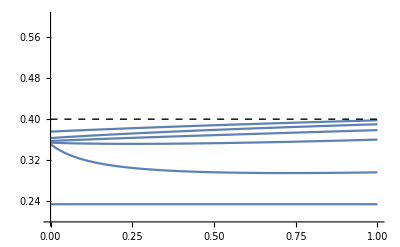

```mathematica
parms={n->3,d->20,b->10,c->1,δ->0.01,p->0.4}
prg={0.2,0.6}
Show[Table[Plot[EXBD/.{Idself->0,Ieself->0,g->0}/.parms/.μ->theμ,{m,0,1},PlotRange->prg],{theμ,{0,0.01,0.05,0.1,0.2,0.5}}],Plot[p/.parms,{m,0,1},PlotStyle->{Thin,Black,Dashed}]]
```

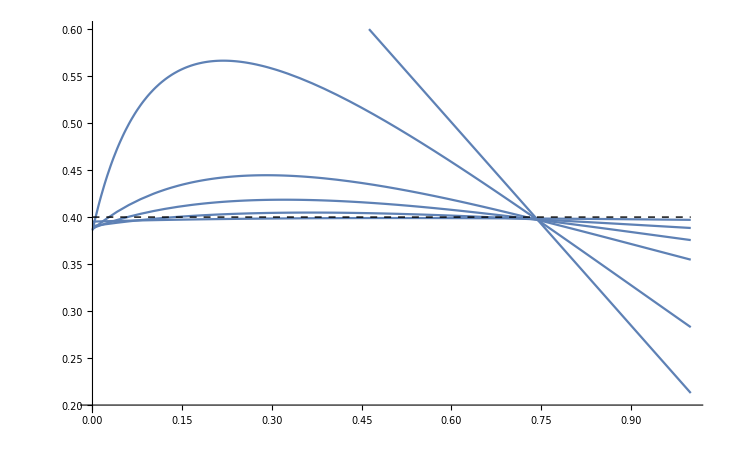

```mathematica
Show[Table[Plot[EXDB/.{Idself->0,Ieself->0,g->0}/.parms/.μ->theμ,{m,0,1},PlotRange->prg],{theμ,{0,0.01,0.05,0.1,0.2,0.5}}],Plot[p/.parms,{m,0,1},PlotStyle->{Thin,Black,Dashed}]]
```

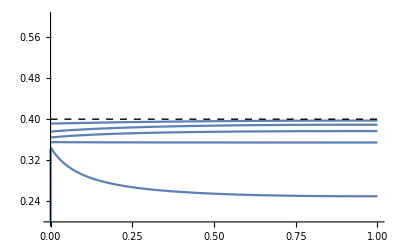

```mathematica
Show[Table[Plot[EXWF/.{Idself->1,Ieself->0,g->0}/.parms/.μ->theμ,{m,0,1},PlotRange->prg],{theμ,{0.000001,0.01,0.05,0.1,0.2,0.5}}],Plot[p/.parms,{m,0,1},PlotStyle->{Thin,Black,Dashed}]]
```

```mathematica
Plot[EXDB[b,c,δ,p,withselfreplacement,groupwithself]/.parms/.μ->0.9,{m,0,1},AxesOrigin->{0,0}]
```

-Graphics-

{n→3,d→4,b→5,c→1,δ→0.05,p→0.4}

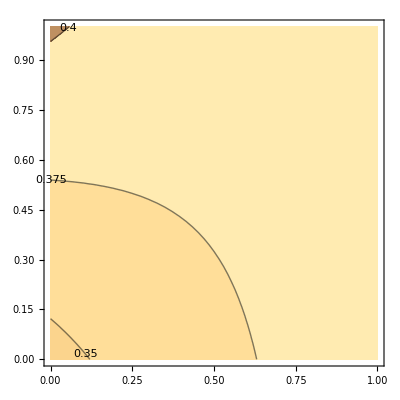

```mathematica
parms={n->3,d->4,b->5,c->1,δ->0.05,p->0.4}
prg={0.2,0.6};ctrs=Table[i,{i,0.2,0.6,0.025}];
ContourPlot[cEXBD[b/.parms,c/.parms,Idself/.Idself->0,Ieself/.Ieself->0,m/.parms,g,n/.parms,d/.parms,μ/.μ->0.5,p/.parms,δ/.parms],{m,0,1},{g,0,1},ContourLabels->True,Contours->ctrs,PlotRange->prg]
```

```mathematica
{{b,_Real},{c,_Real},{Idself,_Integer},{Ieself,_Integer},{m,_Real},{g,_Real},{n,_Integer},{d,_Integer},{μ,_Real},{p,_Real},{δ,_Real}}
```

{{b,_Real},{c,_Real},{Idself,_Integer},{Ieself,_Integer},{m,_Real},{g,_Real},{n,_Integer},{d,_Integer},{μ,_Real},{p,_Real},{δ,_Real}}

### Infinite population

```mathematica
βDB/.genericde/.{Idself->0,Ieself->0}//FullSimplify
```

((1-p) p (Qin-g Qin+g Qout+((-1+m)^2 ((-1+g) (-2+n+(3+(-3+n) n) Qin)-g (-1+n)^2 Qout))/(-1+n)^2+(2 (-1+m) m (g+g (-1+n) Qin+(-1+d-g) n Qout))/((-1+d) n)+(m^2 (-(-1+d-g) (1+(-1+n) Qin)-(2+(-3+d) d+g) n Qout))/((-1+d)^2 n)) (1-μ))/μ

```mathematica
Limit[QinM/.genericde/.Idself->0,d->∞]//FullSimplify
Limit[QinM/.genericde/.Idself->1,d->∞]//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-2+n) (-1+μ)-(-2+n) μ)

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

```mathematica
Limit[QoutM/.genericde,d->∞]//FullSimplify
```

0

```mathematica
βDB/.genericde/.Qout->0
Limit[%,d->∞]//FullSimplify
```

1/μ(1-p) p (((1-g) Ieself)/n+(1-g) (1/(-1+n)-Ieself/((-1+n) n)) (-1+n) Qin-(2 (-1+d) g Idself (1-m) m (1+(-1+n) Qin))/(-n+d n)^2-((-1+d) m^2 n ((1-g) (1/(-1+n)-Ieself/((-1+n) n)) (-1+n)+((1-g) Ieself)/n+((-2+d) g n)/(-n+d n)) (1+(-1+n) Qin))/(-n+d n)^2-(Idself^2 (1-m)^2 (((1-g) Ieself)/n+(1-g) (1/(-1+n)-Ieself/((-1+n) n)) (-1+n) Qin))/n^2-2 (1-m) (1/(-1+n)-Idself/((-1+n) n)) (-1+n) ((Idself (1-m) ((1-g) (1/(-1+n)-Ieself/((-1+n) n))+(1-g) (1/(-1+n)-Ieself/((-1+n) n)) (-2+n) Qin+((1-g) Ieself Qin)/n))/n+((-1+d) m n (g/(-n+d n)+(g (-1+n) Qin)/(-n+d n)))/(-n+d n))-(1-m)^2 (1/(-1+n)-Idself/((-1+n) n))^2 (-1+n) (((1-g) Ieself)/n+((1-g) Ieself (-2+n) Qin)/n+(1-g) (1/(-1+n)-Ieself/((-1+n) n)) (-2+n+(3+(-3+n) n) Qin))) (1-μ)

-((-1+g) (-1+p) p (-(-1+m)^2 (-2+n) n-2 Idself (-1+Ieself) (-1+m)^2 (-1+Qin)+Idself^2 (-1+Ieself) (-1+m)^2 (-1+Qin)+Ieself (m-n) (-2+m+n) (-1+Qin)+n (-2+n-(-2+m) m (3+(-3+n) n)) Qin) (-1+μ))/((-1+n)^2 n μ)

```mathematica
%/.Ieself->0//FullSimplify
```

((-1+g) (-1+p) p ((-1+m)^2 (-2+n) n-2 Idself (-1+m)^2 (-1+Qin)+Idself^2 (-1+m)^2 (-1+Qin)+n (2-n+(-2+m) m (3+(-3+n) n)) Qin) (-1+μ))/((-1+n)^2 n μ)

```mathematica
%/.Idself->0//FullSimplify
%/.g->0//FullSimplify
```

((-1+g) (-1+p) p ((-1+m)^2 (-2+n)+(2-n+(-2+m) m (3+(-3+n) n)) Qin) (-1+μ))/((-1+n)^2 μ)

-((-1+p) p ((-1+m)^2 (-2+n)+(2-n+(-2+m) m (3+(-3+n) n)) Qin) (-1+μ))/((-1+n)^2 μ)

```mathematica
tQinM=Limit[QinM/.genericde/.{Idself->0},d->∞]
```

(-1+m+μ-m μ)/(-1+m (-2+n) (-1+μ)-(-2+n) μ)

```mathematica
ppp=Flatten[{Qout->0,Ieself->0,g->0,Idself->0}]
tD=Limit[βDBD/.genericde/.ppp,d->∞]//FullSimplify
tI=Limit[βDBI/.genericde/.ppp,d->∞]//FullSimplify
```

{Qout→0,Ieself→0,g→0,Idself→0}

Qin-Qin μ

-((-1+m)^2 (-2+n+(3+(-3+n) n) Qin) (-1+μ))/(-1+n)^2

```mathematica
ttD=tD/.Qin->tQinM//FullSimplify
ttI=tI/.Qin->tQinM//FullSimplify
```

((-1+m) (-1+μ)^2)/(-1+m (-2+n) (-1+μ)-(-2+n) μ)

((-1+m)^2 (-1+n+m (-1+μ)-μ) (-1+μ))/((-1+n) (-1+m (-2+n) (-1+μ)-(-2+n) μ))

```mathematica
Limit[ttD,μ->0]//FullSimplify
Limit[ttI,μ->0]//FullSimplify
```

(1-m)/(1+m (-2+n))

((-1+m)^2 (-1-m+n))/((1+m (-2+n)) (-1+n))

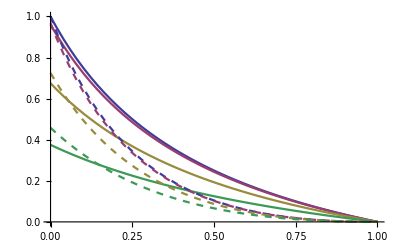

```mathematica
then=4;
μs={0,0.01,0.1,0.25};
nμ=Length[μs];
cols=ColorData[1,"ColorList"];
Show[Table[Plot[ttD/.n->then/.μ->μs⟦iμ⟧,{m,0,1},PlotStyle->cols⟦iμ⟧],{iμ,1,nμ}],
Table[Plot[ttI/.n->then/.μ->μs⟦iμ⟧,{m,0,1},PlotStyle->{Dashed,cols⟦iμ⟧}],{iμ,1,nμ}],
PlotRange->All]
```

```mathematica
Color
```

Color

## Explanations for the paper

### BD

#### Calculations

```mathematica
lBD=Limit[p+δ(βBD b - γBD c)/.genericde/.{Idself->1, Ieself->0,g->0}//FullSimplify,d->∞]//FullSimplify
```

(p (n μ-b (-1+p) δ (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)+c (-1+p) δ (-1+n+Qin+m (1+(-1+n) Qin-n Qout)-n (Qin+μ-Qout μ))))/(n μ)

Q and orders of limits

```mathematica
Limit[QinM/.genericde,d->∞]
Limit[%,μ->0]//FullSimplify

Limit[QinM/.genericde,μ->0]
Limit[%,d->∞]
```

((-1+m) (Idself-n) (-1+μ))/(Idself (-1+m) (-1+μ)+n (-1+m (-2+n) (-1+μ)+2 μ-n μ))

((-1+m) (Idself-n))/(Idself (-1+m)+n+m (-2+n) n)

1

1

```mathematica
lQinM=Limit[QinM/.genericde,d->∞]//FullSimplify
lQoutM=Limit[QoutM/.genericde,d->∞]
```

((-1+m) (Idself-n) (-1+μ))/(-n+(-2+n) n (m (-1+μ)-μ)+Idself (-1+m) (-1+μ))

0

```mathematica
lBD/.Qout->lQoutM//FullSimplify
```

(p (n μ-b (-1+p) δ (-1+m+Qin+m (-1+n) Qin-n Qin μ)+c (-1+p) δ (-1+m+n+Qin+m (-1+n) Qin-n (Qin+μ))))/(n μ)

```mathematica
βBD/.genericde/.{Idself->1, Ieself->0,g->0}//FullSimplify
Limit[%/.Qout->lQoutM,d->∞]//FullSimplify
```

((-1+p) p ((-1+Qin-n Qin+n Qout) μ-d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)))/(d n μ)

-((-1+p) p (-1+m+Qin+m (-1+n) Qin-n Qin μ))/(n μ)

```mathematica
InfLimitM[x_]:=Limit[x/.genericde/.{Idself->1, Ieself->0,g->0}/.Qout->0,d->∞]//FullSimplify
```

```mathematica
βBDD//InfLimitM
βBDI//InfLimitM
```

Qin-Qin μ

-((-1+m) (1+(-1+n) Qin))/n

```mathematica
lQinM/.Idself->1//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

```mathematica
βBD-factorBD(βBDD-βBDI)//FullSimplify
```

0

```mathematica
lEXBD=EXBD//InfLimitM
```

-(p (c m n (-1+p) δ+μ+(m (-1+n)-(2 (b-c) (-1+m)+c (-1+2 m) n) (-1+p) δ) μ+(-1+m) (1-n+(b+c (-1+n)) (-1+p) δ) μ^2))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

```mathematica
dlEXBD=D[lEXBD,m]//FullSimplify
```

(n (-1+p) p δ (c+b (-2+μ) μ))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ)^2)

```mathematica
Solve[dlEXBD==0,μ]//FullSimplify
lμcrit=μ/.%⟦2⟧
```

{{μ→1+(√(b (b-c) (-1+p)^2))/(b-b p)},{μ→1+(√(b (b-c) (-1+p)^2))/(b (-1+p))}}

1+(√(b (b-c) (-1+p)^2))/(b (-1+p))

```mathematica
lμcrit-(1-(√(b-c))/(√b))//FullSimplify
```

(√(b-c))/(√b)+(√(b (b-c) (-1+p)^2))/(b (-1+p))

```mathematica
{1+(√(b (b-c) (-1+p)^2))/(b (-1+p)),1-(√(b-c))/(√b),1-√(1-c/b)}/.{p->0.45,b->15,c->1}//N
```

{0.0339082,0.0339082,0.0339082}

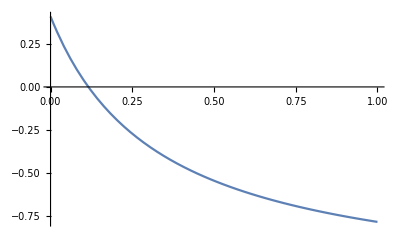

```mathematica
Plot[lEXBD/.{p->0.45,b->15,c->1,n->4,μ->0.001,δ->0.005},{m,0,1}]
```

#### Order of limits

```mathematica
OrderOfLimits[x_]:=Module[{l1,l2},l1=Limit[Limit[x,μ->0],d->∞]//FullSimplify;l2=Limit[Limit[x,d->∞],μ->0]//FullSimplify;{l1,l2}]
```

```mathematica
OrderOfLimits[EXBD/.{Idself->1,Ieself->0}]
```

{c n (-1+p) p δ ∞,p DirectedInfinity[-Sign[c m n (-1+p) δ]/Sign[-1+m-m n]]}

#### Summary

βBDD = Qin (1 - μ);

βBDI=((1-m) (1+(n-1) Qin))/n=(1-m) Qin0
where Qin0 includes the focal.

```mathematica
(EXBD-p)/.δ->ω delta/.μ->ω mu/.d->1/ω
Limit[%,ω->0]//FullSimplify
dexbd=%/.{Idself->1,Ieself->0,g->0}
```

-p+(p ω ((b-c) delta mu (-1+p) ω^2 (m-n+mu ω-m mu ω+Idself (-1+m) (-1+mu ω))+1/ω^2(Idself mu ω-Idself m mu ω-c delta Idself m n ω-c delta m^2 n ω+c delta Idself m^2 n ω-mu n ω+2 m mu n ω+c delta m n^2 ω-m mu n^2 ω+c delta Idself m n p ω+c delta m^2 n p ω-c delta Idself m^2 n p ω-c delta m n^2 p ω+2 c delta Idself mu ω^2-2 c delta Idself m mu ω^2-Idself mu^2 ω^2+Idself m mu^2 ω^2-2 c delta mu n ω^2-c delta Idself mu n ω^2+2 c delta m mu n ω^2+2 c delta Idself m mu n ω^2+c delta m^2 mu n ω^2-c delta Idself m^2 mu n ω^2+2 mu^2 n ω^2-2 m mu^2 n ω^2+c delta mu n^2 ω^2-2 c delta m mu n^2 ω^2-mu^2 n^2 ω^2+m mu^2 n^2 ω^2-2 c delta Idself mu p ω^2+2 c delta Idself m mu p ω^2+2 c delta mu n p ω^2+c delta Idself mu n p ω^2-2 c delta m mu n p ω^2-2 c delta Idself m mu n p ω^2-c delta m^2 mu n p ω^2+c delta Idself m^2 mu n p ω^2-c delta mu n^2 p ω^2+2 c delta m mu n^2 p ω^2-c delta Idself mu^2 ω^3+c delta Idself m mu^2 ω^3+2 c delta mu^2 n ω^3-2 c delta m mu^2 n ω^3-c delta mu^2 n^2 ω^3+c delta m mu^2 n^2 ω^3+c delta Idself mu^2 p ω^3-c delta Idself m mu^2 p ω^3-2 c delta mu^2 n p ω^3+2 c delta m mu^2 n p ω^3+c delta mu^2 n^2 p ω^3-c delta m mu^2 n^2 p ω^3+b delta (-1+g) (-1+p) ω ((-1+m) mu n ω (-2+mu ω)-Ieself (-mu ω+m (-1+mu ω)) (m-mu ω+n (-1+mu ω))+Idself (-1+m) (-mu ω (-2+mu ω)+Ieself (-mu ω+m (-1+mu ω)))))+1/ω(m^2 (-1+mu ω) (-1+mu ω+c delta (-1+p) ω+b (delta ω-delta p ω))+m (n (-(-1+mu ω) (-1+c delta (-1+p) ω)+b (delta ω-delta p ω))-delta mu (-1+p) ω^2 (2 c (-1+mu ω)+b (2-Ieself-2 mu ω+g (-2+Ieself+mu ω))))+Idself (-1+m) (m (-1+mu ω) (1-mu ω+b delta (-1+p) ω+c (delta ω-delta p ω))+mu ω (1-mu ω+c delta (-1+p) ω (-3+n+2 mu ω)+b delta (-1+p) ω (3-Ieself-2 mu ω+g (-2+Ieself+mu ω))))+mu ω (delta (c+b (-1+(-1+g) Ieself)) mu (-1+p) ω^2+n^2 (mu ω+c delta ω (-1+p+mu ω-mu p ω))+n (1+3 c delta ω-2 mu ω-3 c delta p ω-2 c delta mu ω^2+2 c delta mu p ω^2-b delta (-1+p) ω (-3+Ieself+mu ω-Ieself mu ω+g (2-mu ω+Ieself (-1+mu ω))))))))/(m (1+mu (-2+n)) n (-1+mu ω)+m^2 (-1+mu ω)^2-mu n (-1+1/ω) ω (1+mu (-2+n) ω)-Idself (-1+m) (-1+mu ω) (-mu+mu ω+m (-1+mu ω)))

(delta m (Idself (-1+m)-m+n) (b (-1+g) Ieself+c n) (-1+p) p)/(-m^2+Idself (-1+m) (m+mu)+mu n+m (1+mu (-2+n)) n)

(c delta m (-1+n) n (-1+p) p)/(-m^2+(-1+m) (m+mu)+mu n+m (1+mu (-2+n)) n)

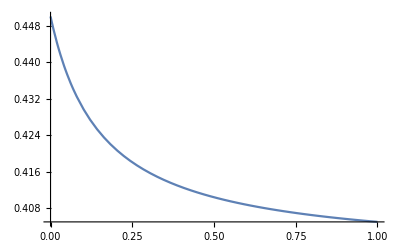

```mathematica
Plot[p+dexbd/.{p->0.45,c->1,n->4,mu->0.3,delta->0.1},{m,0,1}]
```

```mathematica
dmyEXBD=EXBD-p/.{Idself->1,Ieself->0,g->0}//FullSimplify
```

((-1+p) p δ (-d m (b+c (-1+d n))+((b-c) (-1+d (3+2 d (-1+m)))+c d (1+d (-1+2 m)) n) μ-d (1+d (-1+m)) (b+c (-1+n)) μ^2))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

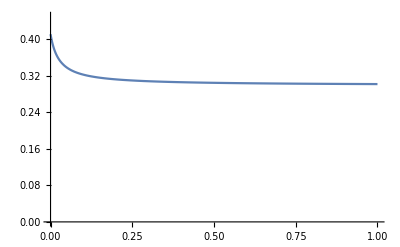

```mathematica
Plot[p+dmyEXBD/.{p->0.45,b->15,c->1,μ-> 0.001,n->4,d->30,δ->0.005},{m,0,1},PlotRange->{0,0.45}]
```

```mathematica
dmyEXBD
```

((-1+p) p δ (-d m (b+c (-1+d n))+((b-c) (-1+d (3+2 d (-1+m)))+c d (1+d (-1+2 m)) n) μ-d (1+d (-1+m)) (b+c (-1+n)) μ^2))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
0
```

0

```mathematica
Series[%,{ω,0,1}]//FullSimplify
%/.{g->0,Ieself->0}
%
```

0

0

0

```mathematica
Limit[EXBD-p,μ->0]/.Ieself->0/.d->dd/ϵ/.δ->δ ϵ^2
Normal[Series[%,{ϵ,0,1}]]//FullSimplify
```

(-1+p) p δ (b+c (-1+(dd n)/ϵ)) ϵ^2

c dd n (-1+p) p δ ϵ

```mathematica
Limit[Limit[EXBD,d->∞],μ->0]
```

p DirectedInfinity[Sign[m (Idself (-1+m)-m+n) (b (-1+g) Ieself+c n) (-1+p) δ]/Sign[Idself (-1+m)+(1+m (-2+n)) n]]

```mathematica
Limit[lEXBD,μ->0]
```

p DirectedInfinity[-Sign[c m n (-1+p) δ]/Sign[-1+m-m n]]

```mathematica
lβBDI
```

lβBDI

```mathematica
factorBD
```

((1-p) p)/μ

```mathematica
lEXBD
```

-(p (c m n (-1+p) δ+μ+(m (-1+n)-(2 (b-c) (-1+m)+c (-1+2 m) n) (-1+p) δ) μ+(-1+m) (1-n+(b+c (-1+n)) (-1+p) δ) μ^2))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

### WF

```mathematica
qq=QinWF/.genericde//FullSimplify
```

((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

```mathematica
Limit[qq,μ->0]
```

```mathematica
Limit[qq,d->∞]//FullSimplify
Limit[%,μ->0]/.Idself->1//FullSimplify
```

((-1+m)^2 (Idself-n) (-2+Idself+n) (-1+μ)^2)/(-2 Idself (-1+m)^2 (-1+μ)^2+Idself^2 (-1+m)^2 (-1+μ)^2+n (2-n-2 m (3+(-3+n) n) (-1+μ)^2+m^2 (3+(-3+n) n) (-1+μ)^2-6 μ+μ ((-3+n) n (-2+μ)+3 μ)))

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
βWF/.
```

1/μ(1-p) p (eself+ein (-1+n) Qin+(-1+d) eout n Qout-dself^2 (eself+ein (-1+n) Qin+(-1+d) eout n Qout)-din^2 (-1+n) (eself+eself (-2+n) Qin+ein (-2+n+(3+(-3+n) n) Qin)+(-1+d) eout (-1+n) n Qout)-(-1+d) dout^2 n ((eself+ein (-1+n)+(-2+d) eout n) (1+(-1+n) Qin)+n ((-2+d) eself+(-2+d) ein (-1+n)+(3+(-3+d) d) eout n) Qout)-2 (-1+d) dout dself n ((eself+ein (-1+n)) Qout+eout (1+(-1+n) Qin+(-2+d) n Qout))-2 din (-1+n) (dself (ein+eself Qin+ein (-2+n) Qin+(-1+d) eout n Qout)+(-1+d) dout n (eout+eout (-1+n) Qin+(eself+ein (-1+n)+(-2+d) eout n) Qout))) (1-μ)

```mathematica
OrderOfLimits[EXWF/.{Idself->1,Ieself->0}]
```

{c n (-1+p) p δ ∞,p DirectedInfinity[Sign[c (-2+m) m n (-1+p) δ]/Sign[-1+(-2+m) m (-1+n)]]}

```mathematica
sEXWF=EXWF/.{Idself->1,Ieself->0}//Simplify
```

-((p (-(-1+d)^2 (-2+μ) μ (-1+2 μ-2 n μ-μ^2+n μ^2+b (-1+g) (-1+p) δ (2-3 μ+μ^2)-c (-1+n) (-1+p) δ (2-3 μ+μ^2))+2 (-1+d) m (-1+μ) (b (-1+p) δ (-2+μ) (-1+d (-1+g) (-2+μ) μ)+(-1+μ) (-1+d (-1+n) (-2+μ) μ)-c (-1+p) δ (-2+μ) (-1+d (n (-1+μ)^2-(-2+μ) μ)))-d m^2 (-1+μ) (b (-1+p) δ (-2+μ) (-1+d (-1+g) (-2+μ) μ)+(-1+μ) (-1+d (-1+n) (-2+μ) μ)-c (-1+p) δ (-2+μ) (-1+d (n (-1+μ)^2-(-2+μ) μ)))))/(-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+(-1+d)^2 (-2+μ) μ (-1-2 (-1+n) μ+(-1+n) μ^2)))

```mathematica
Limit[sEXWF/.{δ->ϵ^2 delta, d->dd/ϵ,μ->ϵ mu}//Simplify,ϵ->0]
ssWF=Limit[sEXWF/.{δ->ϵ delta, d->dd/ϵ,μ->ϵ mu}//Simplify,ϵ->0]//FullSimplify
```

p

```mathematica
sdWF=Limit[sEXWF/.{δ->ϵ^2 delta, d->dd/ϵ}//Simplify,ϵ->0]//FullSimplify
```

p

```mathematica
sssWF=Series[sEXWF/.{δ->ϵ^2 delta, d->dd/ϵ,μ->ϵ mu},{ϵ,0,1}]//FullSimplify
```

p+(2 c dd delta (-2+m) m n (-1+p) p ϵ)/(-2 dd mu+(-2+m) m (1+2 dd mu (-1+n)))+O[ϵ]^2

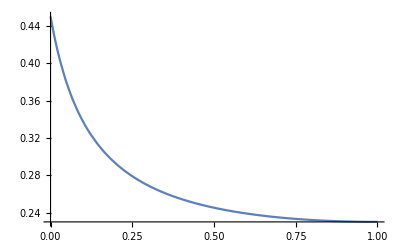

```mathematica
Plot[ssWF/.{p->0.45, b->15,c->1,n->4,ϵ->0.01,dd->1,delta->1,mu->1},{m,0,1},PlotRange->All]
```